```mathematica
Integrate[Exp[-x^(2/3)], x]
```

-3/2 ⅇ^(-x^(2/3)) x^(1/3)+3/4 √π Erf[x^(1/3)]

```mathematica
DSolve[{x^2y''[x]+ 2x y'[x] + (x^2 - l(l + 1) - A x)y[x] == 0}, y[x], x]
```

{{y[x]→ⅇ^(-ⅈ x+l Log[x]) C[1] HypergeometricU[-1/2 ⅈ (2 ⅈ+A+2 ⅈ l),2+2 l,2 ⅈ x]+ⅇ^(-ⅈ x+l Log[x]) C[2] LaguerreL[1/2 ⅈ (2 ⅈ+A+2 ⅈ l),1+2 l,2 ⅈ x]}}

```mathematica
l = 0
MatrixForm[Table[Integrate[x^(2*l + 1)*LaguerreL[n, 2*l + 1, x]*LaguerreL[k, 2*l + 1, x]*
   Exp[-b x], {x, 0, ∞}], {n, 0, 10}, {k, 0, 10}]]
```

0

```mathematica
MatrixForm[Table[1/Factorial[Abs[n - k]] Power[0.1, Abs[n - k]]  Sqrt[Factorial[Min[n, k]]Gamma[2 l + 1 + Max[n, k] + 1]/Factorial[Max[n, k]]/Gamma[2 l + 1 + Min[n, k] + 1]], {n, 0, 10}, {k, 0, 10}]]
```

(1. | 0.141421 | 0.00866025 | 0.000333333 | 9.31695×10^-6 | 2.04124×10^-7 | 3.67465×10^-9 | 5.61196×10^-11 | 7.44048×10^-13 | 8.71439×10^-15 | 9.13973×10^-17
0.141421 | 1. | 0.122474 | 0.00707107 | 0.000263523 | 7.21688×10^-6 | 1.55902×10^-7 | 2.77778×10^-9 | 4.20897×10^-11 | 5.5458×10^-13 | 6.46276×10^-15
0.00866025 | 0.122474 | 1. | 0.11547 | 0.00645497 | 0.000235702 | 6.36469×10^-6 | 1.36083×10^-7 | 2.40563×10^-9 | 3.6225×10^-11 | 4.74914×10^-13
0.000333333 | 0.00707107 | 0.11547 | 1. | 0.111803 | 0.00612372 | 0.000220479 | 5.89256×10^-6 | 1.25×10^-7 | 2.19603×10^-9 | 3.2903×10^-11
9.31695×10^-6 | 0.000263523 | 0.00645497 | 0.111803 | 1. | 0.109545 | 0.00591608 | 0.000210819 | 5.59017×10^-6 | 1.17851×10^-7 | 2.06006×10^-9
2.04124×10^-7 | 7.21688×10^-6 | 0.000235702 | 0.00612372 | 0.109545 | 1. | 0.108012 | 0.0057735 | 0.000204124 | 5.37914×10^-6 | 1.12834×10^-7
3.67465×10^-9 | 1.55902×10^-7 | 6.36469×10^-6 | 0.000220479 | 0.00591608 | 0.108012 | 1. | 0.106904 | 0.00566947 | 0.000199205 | 5.22319×10^-6
5.61196×10^-11 | 2.77778×10^-9 | 1.36083×10^-7 | 5.89256×10^-6 | 0.000210819 | 0.0057735 | 0.106904 | 1. | 0.106066 | 0.00559017 | 0.000195434
7.44048×10^-13 | 4.20897×10^-11 | 2.40563×10^-9 | 1.25×10^-7 | 5.59017×10^-6 | 0.000204124 | 0.00566947 | 0.106066 | 1. | 0.105409 | 0.00552771
8.71439×10^-15 | 5.5458×10^-13 | 3.6225×10^-11 | 2.19603×10^-9 | 1.17851×10^-7 | 5.37914×10^-6 | 0.000199205 | 0.00559017 | 0.105409 | 1. | 0.104881
9.13973×10^-17 | 6.46276×10^-15 | 4.74914×10^-13 | 3.2903×10^-11 | 2.06006×10^-9 | 1.12834×10^-7 | 5.22319×10^-6 | 0.000195434 | 0.00552771 | 0.104881 | 1.)

```mathematica
S=%;
MatrixForm[Table[(l + n + 1) Integrate[x^(2*l + 1)*LaguerreL[n, 2*l + 1, x]*LaguerreL[k, 2*l + 1, x]*
   Exp[- x], {x, 0, ∞}], {n, 0, 10}, {k, 0, 10}]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 36 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 49 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 64 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 81 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 121)

```mathematica
A=%;
```

```mathematica
Eigenvalues[Inverse[A] S]
```

{0.826446,0.348337,0.199504,0.130832,0.0929961,0.0698439,0.0546301,0.0440912,0.0364832,0.0308041,0.0264454}

```mathematica
Table[Integrate[x^(2 l + 1) LaguerreL[n, 2 l + 1, x] Exp[-x], {x, 0, ∞}], {n, 0, 10}]
```

{1,0,0,0,0,0,0,0,0,0,0}

```mathematica
f[a_ , n_, p_ ]:=FunctionExpand[Integrate[x^(a + p) LaguerreL[n, a, x] Exp[-x], {x, 0, ∞}],{ a, n, p} ∈Integers]
```

```mathematica
FullSimplify[f[1,n,p], { p} ∈Integers]
```

∫_0^∞ ⅇ^-x x^(1+p) LaguerreL[n,1,x]ⅆx

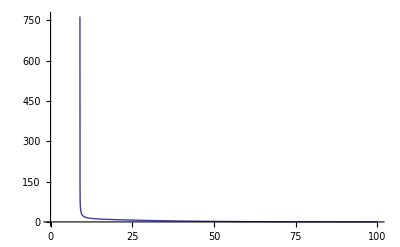

```mathematica
n2[α_, M_, x_] = Sqrt[α x (1 + M x) E^(- M x) / (1 - α / x (1 + M x) E^(- M x))];
Plot[n2[14.6, 0.148, x], {x, 0, 100}, PlotRange->Full]
```